## 出身階層間の教育達成格差

## オッズ比と相対リスク比の比較

```mathematica
(*　オッズ比　と相対リスク比を出力する関数*)
```

```mathematica
edu2[x_,n_,out_]:=Module[{score1,score2,overall,ad,r1,r2,odds,rr},
score1=Table[{RandomReal[NormalDistribution[52,1]],1},{n}];
score2=Table[{RandomReal[NormalDistribution[50,1]],0},{n}];
(*Print["score1=",score1];Print["score2=",score2];*)
overall=Flatten[{score1,score2},1];
overall=Sort[overall,#1[[1]]>#2[[1]]&];
ad=Total[Table[overall[[i]][[2]],{i,1,x}]];
r1=(ad)/(n-ad)(* 上層進学オッズ  *);
r2=(x-ad)/(n-(x-ad))(* 下層進学オッズ *);
odds=r1/r2;(* オッズ比 *)
r1=(ad)/n(* 上層進学率  *);
r2=(x-ad)/n(* 下層進学率 *);
rr=r1/r2;(* 相対リスク比 *)
If[out==0,odds,rr]
]
```

Power::infy: 無限式1/0が見付かりました．

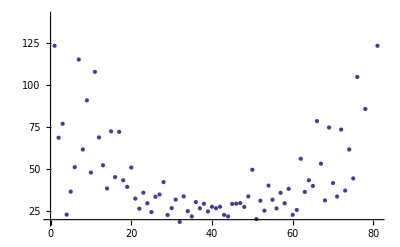

```mathematica
ListPlot[Table[edu2[x,500,0],{x,100,900,10}]]
```

Power::infy: 無限式1/0が見付かりました．

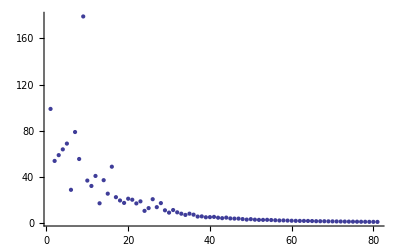

```mathematica
ListPlot[Table[edu2[x,500,1],{x,100,900,10}]]
```

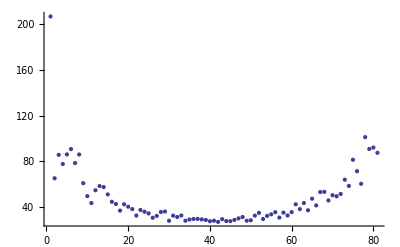

```mathematica
ListPlot[Table[edu2[x,5000,0],{x,1000,9000,100}]]
```

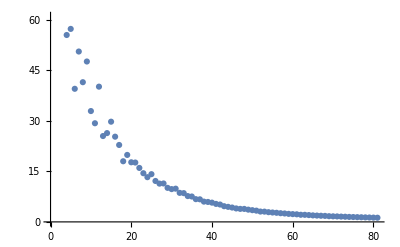

```mathematica
ListPlot[Table[edu2[x,5000(*各人数*),1],{x,1000,9000,100}]]
```

```mathematica
edu3[x_,n_,out_]:=Module[{score1,score2,overall,ad,r1,r2,odds,rr},
score1=Table[{RandomReal[NormalDistribution[52,1]],1},{n}];
score2=Table[{RandomReal[NormalDistribution[50,1]],0},{n}];
(*Print["score1=",score1];Print["score2=",score2];*)
overall=Flatten[{score1,score2},1];
overall=Sort[overall,#1[[1]]>#2[[1]]&];
Print[overall];
ad=Total[Table[overall[[i]][[2]],{i,1,x}]];
Print[ad];
r1=(ad)/(n-ad)(* 上層進学オッズ  *);
r2=(x-ad)/(n-(x-ad))(* 下層進学オッズ *);
odds=r1/r2;(* オッズ比 *)
r1=(ad)/n(* 上層進学率  *);
r2=(x-ad)/n(* 下層進学率 *);
rr=r1/r2;(* 相対リスク比 *)
If[out==0,odds,rr]
]
```

```mathematica
edu3[20,20,0]
```

{{53.0371,1},{52.9457,1},{52.8957,1},{52.6786,1},{52.6144,1},{52.5101,1},{52.2973,1},{52.1683,1},{52.0562,0},{52.0404,1},{51.841,1},{51.8167,1},{51.7505,0},{51.697,1},{51.6087,1},{51.6078,1},{51.5291,1},{51.4445,0},{51.246,0},{51.0365,0},{51.0105,0},{50.8894,0},{50.8006,0},{50.7276,1},{50.7234,0},{50.6842,1},{50.6067,1},{50.5588,1},{50.4014,1},{50.3219,0},{50.1654,0},{49.9906,0},{49.9741,0},{49.8162,0},{49.5294,0},{49.4072,0},{49.4042,0},{49.2854,0},{49.2834,0},{49.2316,0}}

15

9

## プロトタイプ

```mathematica
(*　相対リスク比　*)
edu1[x_,n_]:=Module[{score1,score2,overall,ad,r1,r2},
score1=Table[{RandomReal[NormalDistribution[52,1]],1},{n}];
score2=Table[{RandomReal[NormalDistribution[50,1]],0},{n}];
overall=Flatten[{score1,score2},1];
overall=Sort[overall,#1[[1]]>#2[[1]]&];
(* Print["score1=",score1];Print["score2=",score2];
 compare scores. #[[1]] means score  *)
ad=Table[overall[[i]][[2]],{i,1,x}];
(* Print[ad];Print[r1];Print[r2];上層進学者数 *)
r1=(Total[ad])/n(* 上層進学率  *);
r2=(x-Total[ad])/n(* 下層進学率 *);
N[r1/r2]
]
```

```mathematica
(*  for confirmation with print　  *)
edu20[x_,n_]:=Module[{score1,score2,overall,ad,r1,r2},
score1=Table[{RandomReal[NormalDistribution[52,1]],1},{n}];
score2=Table[{RandomReal[NormalDistribution[50,1]],0},{n}];
(*Print["score1=",score1];Print["score2=",score2];*)
overall=Flatten[{score1,score2},1];
overall=Sort[overall,#1[[1]]>#2[[1]]&];
ad=Table[overall[[i]][[2]],{i,1,x}];
Print[ad];
ad=Total[ad];
r1=(ad)/Max[{(n-ad),0.000001}](* 上層進学オッズ  *);
Print[r1];
r2=(x-ad)/Max[{(n-(x-ad)),0.000001}](* 下層進学オッズ *);
Print[r2];
N[r1/Max[{r2,1^(-6)}]]
]
```

```mathematica
edu21[x_,n_]:=Module[{score1,score2,overall,ad,r1,r2},
score1=Table[{RandomReal[NormalDistribution[52,1]],1},{n}];
score2=Table[{RandomReal[NormalDistribution[50,1]],0},{n}];
(*Print["score1=",score1];Print["score2=",score2];*)
overall=Flatten[{score1,score2},1];
overall=Sort[overall,#1[[1]]>#2[[1]]&];
ad=Table[overall[[i]][[2]],{i,1,x}];
Print[ad];
ad=Total[ad];
r1=(ad)/Max[{(n-ad),1}](* 上層進学オッズ  *);
Print[r1];
r2=(x-ad)/Max[{(n-(x-ad)),1}](* 下層進学オッズ *);
Print[r2];
N[r1/Max[{r2,1}]]
]
```

```mathematica
edu22[x_,n_]:=Module[{score1,score2,overall,ad,r1,r2},
score1=Table[{RandomReal[NormalDistribution[52,1]],1},{n}];
score2=Table[{RandomReal[NormalDistribution[50,1]],0},{n}];
(*Print["score1=",score1];Print["score2=",score2];*)
overall=Flatten[{score1,score2},1];
overall=Sort[overall,#1[[1]]>#2[[1]]&];
ad=Table[overall[[i]][[2]],{i,1,x}];
(*Print[ad];Print[r1];Print[r2];*)
ad=Total[ad];
r1=(ad)/Max[{(n-ad),1}](* 上層進学オッズ  *);
r2=(x-ad)/Max[{(n-(x-ad)),1}](* 下層進学オッズ *);
N[r1/Max[{r2,1}]]
]
```

```mathematica
edu23[x_,n_]:=Module[{score1,score2,overall,ad,r1,r2},
score1=Table[{RandomReal[NormalDistribution[52,1]],1},{n}];
score2=Table[{RandomReal[NormalDistribution[50,1]],0},{n}];
(*Print["score1=",score1];Print["score2=",score2];*)
overall=Flatten[{score1,score2},1];
overall=Sort[overall,#1[[1]]>#2[[1]]&];
ad=Table[overall[[i]][[2]],{i,1,x}];
(*Print[ad];Print[r1];Print[r2];*)
ad=Total[ad];
r1=(ad)/Max[{(n-ad),0.1}](* 上層進学オッズ  *);
r2=(x-ad)/Max[{(n-(x-ad)),0.1}](* 下層進学オッズ *);
N[r1/Max[{r2,0.1}]]
]
```

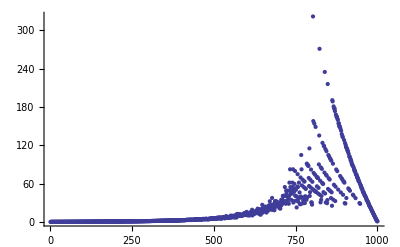

```mathematica
ListPlot[Table[edu22[x,500],{x,1,1000}]]
```

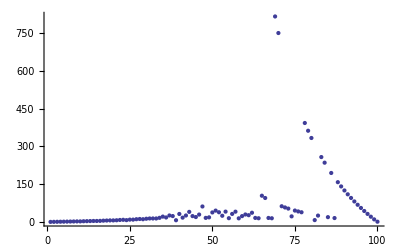

```mathematica
ListPlot[Table[edu23[x,50],{x,1,100}]]
```

Power::infy: 無限式1/0が見付かりました．

General::stop: この計算中に，Powerのこれ以上の出力は表示されません．

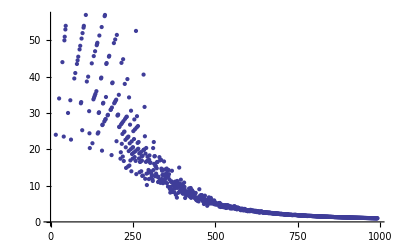

```mathematica
ListPlot[Table[edu1[x,500],{x,10,1000}]]
```

```mathematica
edu20[35,20]
```

{1,1,1,1,0,1,1,1,1,1,1,1,1,0,0,1,1,0,1,0,0,1,1,0,0,1,0,1,0,0,1,0,0,0,0}

2.×10^7

3

6.66667×10^6

```mathematica
edu2[35,20]
```

Power::infy: 無限式1/0が見付かりました．

ComplexInfinity

```mathematica
Table[edu20[x,20],{x,1,40}]
```

{0.0526316,0.111111,0.176471,0.25,0.333333,0.428571,0.428571,0.666667,0.818182,1.,1.,1.22222,1.22222,1.5,1.85714,3.,4.,4.,5.66667,4.,4.,5.66667,3.,2.×10^7,4.,2.×10^7,2.×10^7,19.,2.×10^7,2.×10^7,12.6667,1.33333×10^7,1.07692×10^7,8.57143×10^6,4.75,5.×10^6,3.52941×10^6,2.22222×10^6,1.05263×10^6,1.}

```mathematica
edu[x_,n_]:=Module[{score1,score2,overall,ad,r1,r2,out},
score1=Table[{RandomReal[NormalDistribution[52,1]],1},{n}];
score2=Table[{RandomReal[NormalDistribution[50,1]],0},{n}];
(*Print["score1=",score1];Print["score2=",score2];*)
overall=Flatten[{score1,score2},1];
overall=Sort[overall,#1[[1]]>#2[[1]]&];
ad=Table[overall[[i]][[2]],{i,1,x}];

r1=(Total[ad])/n(* 上層進学率  Print[ad];Print[r1];*);
r2=(x-Total[ad])/n(* 下層進学率 Print[r2];*);
r2=If[r2==0,0.00001,r2];
out=If[(r1/r2)>20,20,N[r1/r2]];
out]
```

General::spell1: スペル間違いの可能性があります．新規シンボル"out"はすでにあるシンボル"Out"に似ています．

```mathematica
Table[edu[x,20],{x,5,40}]
```

{20,20,20,20,8.,20,20,11.,20,20,14.,2.2,16.,17.,5.33333,4.,20.,3.4,2.28571,3.8,3.16667,3.33333,2.,1.8,1.9,2.,1.58333,1.66667,1.53846,1.26667,1.33333,1.25,1.17647,1.11111,1.05263,1.}

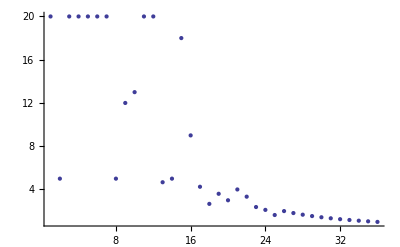

```mathematica
ListPlot[Table[edu[x,20],{x,5,40}]]
```

```mathematica
Max[9,2]
```

9

```mathematica
Module[{x,score1,score2,overall,n=20},x=20;
score1=Table[{RandomReal[NormalDistribution[52,1]],1},{n}];
score2=Table[{RandomReal[NormalDistribution[50,1]],0},{n}];
Print["score1=",score1];
Print["score2=",score2];
overall=Flatten[{score1,score2},1];
overall=Sort[overall,#1[[1]]>#2[[1]]&];
Table[overall[[i]][[2]],{i,1,x}]]
```

score1={{51.7421,1},{50.9857,1},{51.7019,1},{51.0768,1},{53.0902,1},{52.4511,1},{51.7057,1},{51.5571,1},{53.1827,1},{51.8598,1},{52.0315,1},{53.5544,1},{51.3352,1},{51.8459,1},{54.0747,1},{51.6183,1},{50.8751,1},{49.6314,1},{52.7549,1},{52.7282,1}}

score2={{49.5605,0},{48.736,0},{49.0731,0},{52.2103,0},{49.6672,0},{49.1843,0},{50.1265,0},{50.1245,0},{50.8292,0},{49.2313,0},{50.5619,0},{50.6859,0},{49.2923,0},{50.9393,0},{50.4744,0},{48.3895,0},{50.8331,0},{49.0619,0},{48.3379,0},{51.1499,0}}

{1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,0,1,1}

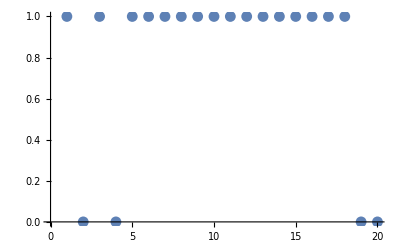

```mathematica
ListPlot[{1,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0}]
```

```mathematica
Show[%2,PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

-Graphics-

```mathematica
edu[x_]:=Module[{score1,score2,overall,n=20},
score1=Table[{RandomReal[NormalDistribution[52,1]],1},{n}];
score2=Table[{RandomReal[NormalDistribution[50,1]],0},{n}];
Print["score1=",score1];
Print["score2=",score2];
overall=Flatten[{score1,score2},1];
overall=Sort[overall,#1[[1]]>#2[[1]]&];
Table[overall[[i]][[2]],{i,1,x}]]
```

```mathematica
edu[15]
```

score1={{53.7303,1},{52.3708,1},{52.3945,1},{51.9645,1},{53.9728,1},{52.3622,1},{52.3018,1},{50.9521,1},{50.5905,1},{52.5791,1},{51.5308,1},{50.324,1},{50.8974,1},{52.3674,1},{51.8116,1},{52.517,1},{53.5231,1},{52.3738,1},{52.9116,1},{52.4038,1}}

score2={{52.1961,0},{51.1302,0},{48.9108,0},{50.9745,0},{48.1613,0},{50.4461,0},{49.8488,0},{50.4898,0},{49.3651,0},{52.9219,0},{50.4541,0},{51.5727,0},{48.4253,0},{49.0219,0},{50.1116,0},{51.2268,0},{50.0576,0},{50.6848,0},{48.0136,0},{48.5239,0}}

{1,1,1,0,1,1,1,1,1,1,1,1,1,1,0}

```mathematica
edu[x_,n_]:=Module[{score1,score2,overall},
score1=Table[{RandomReal[NormalDistribution[52,1]],1},{n}];
score2=Table[{RandomReal[NormalDistribution[50,1]],0},{n}];
Print["score1=",score1];
Print["score2=",score2];
overall=Flatten[{score1,score2},1];
overall=Sort[overall,#1[[1]]>#2[[1]]&];
Table[overall[[i]][[2]],{i,1,x}]]
```

```mathematica
edu[10,30]
```

score1={{51.6312,1},{52.4624,1},{52.4522,1},{52.016,1},{51.2771,1},{52.6784,1},{51.2592,1},{52.0467,1},{53.0464,1},{52.771,1},{53.5706,1},{53.0121,1},{50.9418,1},{51.6199,1},{50.0222,1},{52.986,1},{53.8055,1},{55.056,1},{52.3889,1},{53.5403,1},{52.8745,1},{53.5658,1},{52.148,1},{54.4162,1},{52.8745,1},{51.7389,1},{52.7842,1},{53.0858,1},{51.5659,1},{52.8768,1}}

score2={{51.0289,0},{47.9014,0},{47.3001,0},{51.6498,0},{50.49,0},{48.6154,0},{49.861,0},{49.2586,0},{48.3926,0},{50.4744,0},{49.1208,0},{50.6877,0},{49.7956,0},{48.081,0},{49.207,0},{49.0252,0},{50.966,0},{49.5604,0},{50.1009,0},{50.6772,0},{50.5578,0},{49.3635,0},{50.2633,0},{49.5721,0},{51.0127,0},{49.5433,0},{50.921,0},{47.6341,0},{49.292,0},{50.072,0}}

{1,1,1,1,1,1,1,1,1,1}

```mathematica
edu[10,20]
```

score1={{52.1442,1},{52.7745,1},{50.9059,1},{51.8235,1},{51.121,1},{51.4685,1},{52.7136,1},{51.7497,1},{52.1649,1},{52.7901,1},{52.805,1},{52.0311,1},{51.5814,1},{52.1773,1},{51.5426,1},{51.4505,1},{52.0561,1},{52.1756,1},{52.4514,1},{52.8945,1}}

score2={{50.1934,0},{49.3544,0},{50.5041,0},{48.8895,0},{50.0027,0},{49.4463,0},{49.0741,0},{50.0622,0},{50.0311,0},{50.0609,0},{50.6886,0},{51.3431,0},{51.1684,0},{50.1622,0},{51.1759,0},{51.9395,0},{50.653,0},{49.1772,0},{48.5262,0},{50.6872,0}}

{1,1,1,1,1,1,1,1,1,1}

```mathematica
edu[x_,n_]:=Module[{score1,score2,overall},
score1=Table[{RandomReal[NormalDistribution[52,1]],1},{n}];
score2=Table[{RandomReal[NormalDistribution[50,1]],0},{n}];
(*Print["score1=",score1];Print["score2=",score2];*)
overall=Flatten[{score1,score2},1];
overall=Sort[overall,#1[[1]]>#2[[1]]&];
Table[overall[[i]][[2]],{i,1,x}]]
```

```mathematica
edu[5,30]
```

{1,1,1,1,1}

```mathematica
edu[20,20]
```

score1={{52.3083,1},{51.7831,1},{53.9887,1},{51.0987,1},{51.9372,1},{52.0931,1},{51.4539,1},{51.8391,1},{52.4485,1},{51.3579,1},{50.0121,1},{51.7097,1},{52.2708,1},{52.6382,1},{52.9884,1},{52.6132,1},{52.3216,1},{51.9848,1},{51.8893,1},{50.5518,1}}

score2={{49.0734,0},{50.9702,0},{49.9281,0},{48.7698,0},{52.4692,0},{48.7777,0},{50.2409,0},{49.7481,0},{51.4022,0},{50.2312,0},{50.6131,0},{48.0228,0},{49.3465,0},{50.5372,0},{48.5114,0},{49.706,0},{49.4996,0},{48.0096,0},{50.4455,0},{48.7374,0}}

{1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1}

9/10

1/10

9.